Complete The Wolfram Expression

Baschieri Daniele

Di Virgilio Riccardo

University of Bologna.

Most representative image

-Graphics-

Abstract

GOAL OF THE PROJECT: Design an interactive browser game where you can improve your skill with wolfram language, starting from a topic of your interest the system will show you a Wolfram Expression with a missing part to complete, in a growing of difficulty and fun.

SUMMARY OF WORK: Developing a web application based on Wolfram’s stack technology, focusing on exploring safe examples for the game in a dynamic self configuring context.
Application is ready for a public deployment, but with such a vast number of example more test are required to verify the stability of this alpha release.

RESULTS AND FUTURE  WORK: Application is now available in alpha stage on this link https://wolfr.am/complete-the-function the very next step is the releasing it on the WolframCloud and let it available for everyone. The gamification aspect of the application is really minimal right now, in the future could be useful add badges and karma-point in order to increase the fun and also adding multiple choice in the easy mode in order to balance the difficulty.

Everything above this bar is your poster. Make sure it fits on a single page. "Preview Poster"

Additional concise content for 2 minute presentation

The game is fully developed in Wolfram Mathematica Language, is composed with 3 different component:
The URLDispatcher redirect each http request on the correspondent template, it’s the entry point of the game and the most important part of the application.

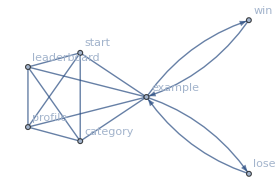

Current graph of the web page that URLDispatcher manage to present.

The second most important aspect of the game is the function that tweak a working wolfram expression and replace a Symbol with a Placeholder. (  1  )

```mathematica
Table[PieChart[{1,2,3},SectorOrigin->θ],{θ,{0,π/4,π/2}}]
```

```mathematica
Table[1[{1,2,3},SectorOrigin->θ],{θ,{0,π/4,π/2}}]
```

During this process is important to pay attention that the expression not evaluate, some Head like Now can produce different output if are not manage correctly.
Finally another section of this project is related with the classification of the exercise and the realization of a subset of instruction that can be used during the game.
Some Expression can be really dangerous for Wolfram Kernel. Expressions like Quit or Import, Export can compromise the Wolfram’s account of the user, so the system is designed to accept only a huge subset of expression and will present only the example form the documentation that contain expression in that’s safe subset.

-Graphics-

The best way to understand better the system is trying it at https://wolfr.am/complete-the-function

Everything above this bar is in your 2 minute presentation. "Preview Presentation"

Detailed Records of the Project

Main Results in Detail

Code

The full source code can be found on GitHub

https://github.com/DangerBlack/WSS17-personal-project/tree/master/Project

The structure of the source code is quiet simple.
In order to run the code you need to use this instruction.

```mathematica
Unprotect[$TemplatePath];
$TemplatePath=Prepend[
					$TemplatePath,
					PacletManager`PacletResource["Project","Assets"]
					];
<<HTTPHandling`
<<Project`
StartWebServer[$CompleteExpressionApp]
```

Code is in the root of the Project folder, in different files:
core.m, whitelist.m are class related with the expression manipulation and retrieval from documentation.
category.m is the class with the accepted Symbols divided by categories.
webview.m is the dispatcher and the entry point of the whole application.
storage.m and settings.m are classes related with saving score in cloud and saving and loading data from the webserver’s machine.

Written Content / Lesson Plans

### Smart use of seed in Random

The development of the web interface leads to develop a restful website in order to do so some effort was spent to make URL consistent.
When a user connect to a specific game the random symbol removed must be always the same, in order to accomplish this we encode the seed of the tweak function in the URL.
When an user request a new exercises http://$AppRoot/category/BasicSymbols/easy/  the system generate a new list containing a list made by 
difficulty seed exerciseId hash 
than redirect the user to a different URL,
for example:
http://$AppRoot/category/BasicSymbols/easy:294:10uwnetq30jhf:1j5e7hz091u8wyhllpctx5q3n04rxsm87l087qfowcxu00qjgo/
We design this system to keep integrity in the request made by the users, but we add the hash of the first tree values in the end in order to prevent that a user can manipulate the random seed and move the missing part and be able to discover the correct answer.

```mathematica
$uuid= "secret string stored in the server";
customHash[expr_,rest___]:=IntegerString[Hash[{expr,$uuid},rest],36]
signList[s_List]:=With[{l=Map[ToString,s]},StringJoin[Riffle[Append[l,customHash[l,"SHA256"]],":"]]]
unsign[{l__,h_}]:=If[MatchQ[customHash[{l},"SHA256"],h],{l},$Failed]
unsign[s_String]:=unsign[StringSplit[s,":"]]
unsign[__]:=$Failed
s=signList[{"easy",294,"10uwnetq30jhf"}]
unsign [s]
```

easy:294:10uwnetq30jhf:4jww2nqwqvud5jtu7r2mkepojfzbq0dwd8uebxo7zfzjqrp9zk

{easy,294,10uwnetq30jhf}

```mathematica
(* if we try to manipulate the seed in order to tweak different expression*)
unsign["easy:42:10uwnetq30jhf:4jww2nqwqvud5jtu7r2mkepojfzbq0dwd8uebxo7zfzjqrp9zk"]
```

$Failed

```mathematica
Multiple answer for a specific question
```

Wolfram Mathematica languages have a huge amount of function in his core and some of them can be used mutually to solve the same problem.

```mathematica
With[{Set[x,3]},x+5]
With[{SetDelayed[y,3]},y+5]
```

8

8

In order to prevent false negative by checking only the user input it has been implemented a smart function that check victory from the output of the problem.

```mathematica
victoryChecker[difficulty_,
			seed_,
			exId_,
			expression_,
			response_,
			urlWin_,
			urlLose_]:=If[MatchQ[Values[getSolution[expression]],Values[response]],
(
	addPoint[difficulty,seed,exId,calculateScore[difficulty,seed,exId]];
	HTTPRedirect[urlWin]
),
If[SubsetQ[$wholewhitelist,Values@response],With[{number=RandomInteger[{1,1000000}]},
(
SeedRandom[number];
res1=Identity@@@$DataBase["Examples"][exId];
SeedRandom[number];
res2=Check[Identity@@@relaseAllPlaceholder[expression,Echo@Map[ToExpression[#,StandardForm]&,Echo@Values@response]],$superPrideFailSoRainbow];
If[res1===res2,
(
addPoint[difficulty,seed,exId,calculateScore[difficulty,seed,exId]];
HTTPRedirect[urlWin]
),HTTPRedirect[urlLose]]
)
],
HTTPRedirect[urlLose]]
]
```

This function redirect the user to a victory page if the Head inserted match with the one removed by the system or if not try to compare the output of the computation if and only if the Symbol inserted by the user is in the safe Symbol subset. ($wholewhitelist)

```mathematica
Atomic expression and removing head
```

During the development of the software some function present a wrong behavior for example, Images from documentation like:

```mathematica
Image[{{0.1,0.2,0.3},{0.4,0.5,0.6},{0.7,0.7,0.9}}]
```

-Graphics-

Basically an Image is just a List of List and this could leads to trouble if we just apply a tweak function on an object like this, because tweak traverse the whole tree can break the Image making it hard to understood from the user what is meant to be in the end.

```mathematica
ImageCompose[-Graphics-,-Graphics-]//FullForm
```

Image[RawArray["Real64",List[List[List[0.,0.,0.,0.],List[0.,0.,0.,0.],List[0.,0.,0.,0.],List[0.,0.,0.,0.],List[0.,0.,0.,0.],50,List[0.,0.,0.,0.],List[0.,0.,0.,0.],List[0.,0.,0.,0.],List[0.,0.,0.,0.],List[0.,0.,0.,0.]],58,List[1]]],2,1]
 |  |  |  |

With this example is more clear that an expression like this should be consider as atomic.

```mathematica
AtomQ[-Graphics-]
```

True

So it have been decided to keep unaltered some expressions like Image or Random*, only to maintain the game experience enjoyable and presents code as people are used to see.
It’s an important aspect on learning coding skill, the possibility of doing exercises in an “ecological” environment. For ecological environment is intended a real situation and not a well crafted or to much artefact learning experience.

```mathematica
removeExpressionPart[expr_,patt___]:=With[{pattern=Alternatives[_Image,_Graph,_Graphics,_Graphics3D,_Random,_RandomWord,_RandomInteger,_RandomReal,_RandomChoice,_RandomSample,List,Rule,RuleDelayed,patt]
},expr/.pattern->garbage]
```

```mathematica
removeExpressionPart[Hold[ImageCompose[-Graphics-,-Graphics-]]]
```

Hold[ImageCompose[garbage,garbage]]

As you can see the system remove the two images and replace them with a placeholder named garbage.

Classification of expressions between different categories

During this project it had been encountered a lot of  difficulties in classify the different function of the Wolfram languages. 
First approach starts from a book of Stephen Wolfram: An elementary introduction to the Wolfram Language the notebook was imported and the function that occur in each expression where divided by the category suggested by the book.
Those work leads to a first draft of safe and easy Symbols that represent different categories. But despite the fact that the book is really useful for learning Wolfram languages has very few Symbols because is meant to be a book for beginner. So each category was expanded by downloading from the documentation each example from the Symbols in the category and than extracting all the Symbols of each expression retrieved.
This create the dataset contained in categories.m a very good starting point for the project because each Symbol is safe and do not have dangerous side effects but absolutely not useful for splitting exercise in different category.
After some work and some refactoring a function from the documentation solve the problem.

```mathematica
newCatByFun=First/@
	DeleteMissing[
	AssociationMap[
		WolframLanguageData[#,"FunctionalityAreas"]&,
		$wholewhitelist]
	]
```

This function retrieve the category of each Symbols presents in the $wholewhitelist and create an Association with it.
After this step some Functionality Areas are low populated and got manually joined in macro areas.
This leads to  a macro category named Basic Symbols and other categories with at least 40 Symbols.

Conclusions in Detail

During this project a web services have been created, the whole process was really useful for me to understand better the wolfram languages and its new functionality for CloudDeployment.
The project is now working well locally but an error was discovered in the 11.1 version of the wolfram kernel that do not let deploy the $CompleteExpressionApp on the Cloud.
The error occur when you try to traverse a link in the deployed object the system keep redirecting you to core page or to 404 page.
Future release of Mathematica should fix this issue.
All the software developed are available online in the GitHub page.

All Visualizations

Data Sources Links/References

Future Directions

The very next step should be adding badges for completing a certain amount of exercise of each category and in general increase the gamification aspects of the games.
Adding social buttons for sharing your results or the most difficult expressions can lead to a better diffusion of the game and expand his bounds.
Another interesting aspect we should consider is Karma point a sort of incentive to user to explore new unknown topic or to make longer session of training.
Another important aspect is to make a full usability testing of the application for removing bug in the interface and make easier for user to use the app without any training. A quick fix for the High difficulty where two Head are removed is to use meaningful color for pairing the empty spot and the Input field.

Background Info Links/References

Web application structure and Package structure, https://github.com/riccardodivirgilio/starthere Riccardo di Virgilio, 2017

Based on an old version of the game named Find the bug, Vitaliy Kaurov

Keywords

Games

Educations

Wolfram Languages

Meta Languages manipulations

Web Application

Clouds

Other

Date

Last Modified: Monday, July 03, 2017

```mathematica
"Add Timestamp"
```